# Vergleich von G0SEG0 für Fröhlich Polaron

## Import

```mathematica
SetDirectory["/project/theorie/h/H.Guertner/BEC_Polaron/Mathematica/"];
<< params.mx;
ResetDirectory[];
p =Import["DiagMC_BEC.json", {"Data", "Momentum"} ];
μ = Import["DiagMC_BEC.json", {"Data", "Chemical_Potential"} ];
```

```mathematica
peter=Import["/home/h/H.Guertner/theorie/BEC_Polaron/peter/FP_all", "Table"];
peter = Insert [peter, {0,1,0}, 1];
peter1=Import["/home/h/H.Guertner/theorie/BEC_Polaron/peter/FP_1", "Table"];
peter1 = Insert [peter1, {0,0,0}, 1];
data=Import["data/all_orders", "Table"];
data = Insert [data, {0,1,0}, 1];
data1= Import["data/first_order", "Table"];
data1 = Insert [data1, {0,0,0}, 1];
```

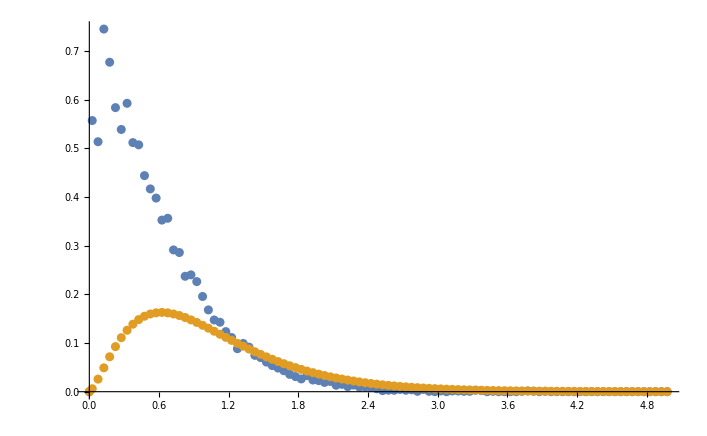

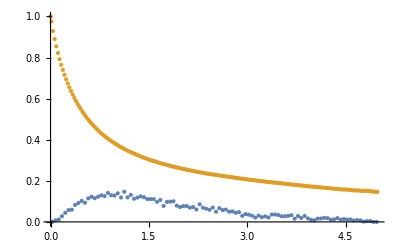

```mathematica
ListPlot[{data1[[All,1;;2]], peter1[[All,1;;2]]}, PlotRange->Full]
ListPlot[{data[[All,1;;2]], peter[[All,1;;2]]}, PlotRange->Full]
```

## First Order FT Hans

```mathematica
(*Interpolation*)
interpolg0seg01 = Interpolation[data1[[All,1;;2]]];
interpolg0seg01w[w_]:= NIntegrate[interpolg0se1[t]*Exp[I*w*t], {t, 0, 4.99}];
interpolg0se1w[w_] := interpolg0seg01w[w]/g0pw[p, I w, 0];
(*Simpson*)

h1st= (data1[[3, 1]]-data1[[2, 1]])/3;
lpf1st[itau_, ω_] := data1[[itau, 2]]*Exp[I*ω*data1[[itau, 1]]];
g0seg01st[ω_] := h1st*(lpf1st[1, ω]+lpf1st[-1, ω]+ Sum[4*lpf1st[itau, ω], {itau, 2, Length[data1]-1, 2}] + Sum[2*lpf1st[itau, ω], {itau, 3, Length[data1]-2, 2}]); 
g0se1st[w_] := g0seg01st[w]/g0pw[p, I w, 0];
```

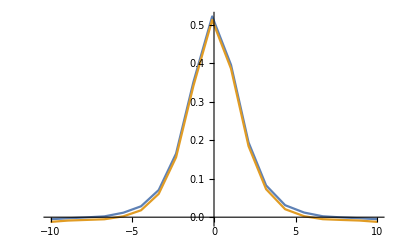

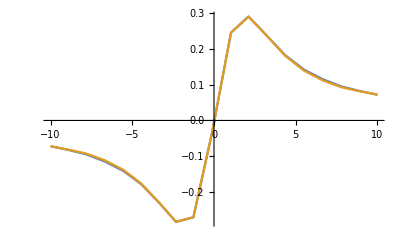

```mathematica
Plot[{Re[g0se1st[w]], Re[interpolg0se1w[w]]}, {w, -10,10}, PlotPoints->10, MaxRecursion->1, PlotRange->Full]
Plot[{Im[g0se1st[w]], Im[interpolg0se1w[w]]}, {w, -10,10}, PlotPoints->10, MaxRecursion->1, PlotRange->Full]
```

## All orders FT Hans

```mathematica
(*Interpolation*)
interpolg0se = Interpolation[data[[All,1;;2]]];
interpolg0sew[w_]:= NIntegrate[interpolg0se[t]*Exp[I*w*t], {t, 0, 4.99}];
interpolg0sewtot[w_] :=interpolg0sew[w]+ interpolg0se1w[w];
```

```mathematica
(*Simpson*)
h= (data[[3, 1]]-data[[2, 1]])/3;
lpf[itau_, ω_] := data[[itau, 2]]*Exp[I*ω*data[[itau, 1]]];
g0sebig2nd[ω_] := h(lpf[1, ω]+lpf[-1, ω]+ Sum[4*lpf[itau, ω], {itau, 2, Length[data]-1, 2}] + Sum[2*lpf[itau, ω], {itau, 3, Length[data]-2, 2}]); 
g0se[ω_] := g0se1st[ω]+g0sebig2nd[ω];
```

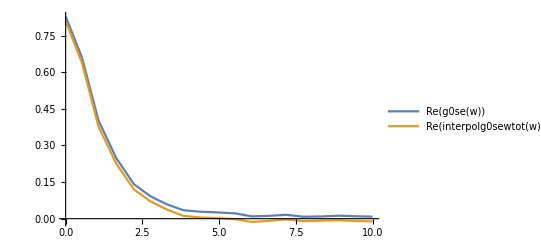

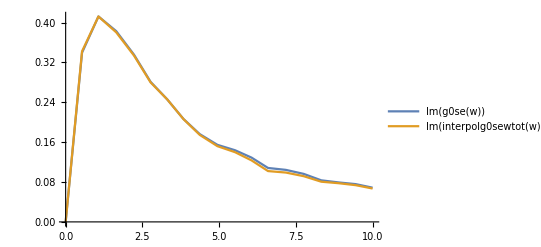

```mathematica
Plot[{Re[g0se[w]], Re[interpolg0sewtot[w]]}, {w,0,10}, PlotRange -> Full,PlotPoints->10, MaxRecursion->1, PlotLegends->"Expressions"]
Plot[{Im[g0se[w]], Im[interpolg0sewtot[w]]}, {w,0,10}, PlotRange -> Full,PlotPoints->10, MaxRecursion->1, PlotLegends->"Expressions"]
```

## Combination to get G-G0 Hans

```mathematica
gminusg0w[ω_]:= g0pw[p, I ω, 0]*(g0se[ω]/(1-g0se[ω]));
interpolgminusg0w[w_]:= g0pw[p, I w, 0]*(interpolg0sewtot[w]/(1-interpolg0sewtot[w]));
```

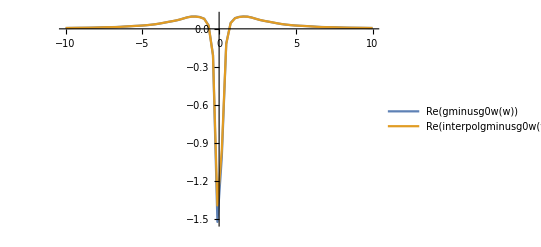

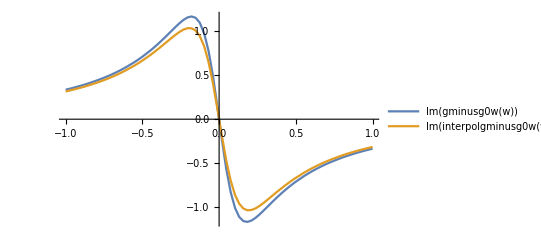

```mathematica
Plot[{Re[gminusg0w[w]], Re[interpolgminusg0w[w]]}, {w,-10,10}, PlotRange -> Full,PlotPoints->10, MaxRecursion->3, PlotLegends->"Expressions"]
Plot[{Im[gminusg0w[w]], Im[interpolgminusg0w[w]]}, {w,-1,1}, PlotRange -> Full,PlotPoints->10, MaxRecursion->3, PlotLegends->"Expressions"]
```

## All orders G-G0 Peter for 0<tau<infinity

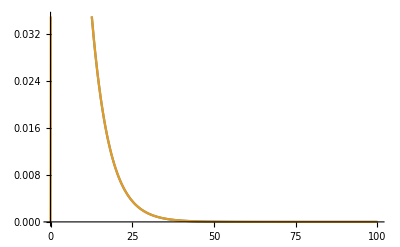

```mathematica
gip:= Interpolation[peter[[All,1;;2]]];
ginffit= FindFit[peter[[100;; ,1;;2]], zfit*Exp[-(Efit-μ )*t], {zfit,Efit}, t];
z=zfit/.ginffit[[1]];
e=Efit/.ginffit[[2]];
ginfbla[t_]:= z*Exp[-(e-μ )*t]
gtotpeter[t_]:=If[t<5,gip[t],ginfbla[t]];
gminusg0peter[t_]:= gtotpeter[t]- g0[p,0,t];
Plot[{gtotpeter[t], gminusg0peter[t]}, {t,0,100}]
```

## G ReFT Hans

```mathematica
gminusg0[t_]:= NIntegrate[1/2/Pi*gminusg0w[w]*Exp[-(I *w*t)], {w, -10,10}];
interpolgminusg0[t_]:= NIntegrate[1/2/Pi*interpolgminusg0w[w]*Exp[-(I *w*t)], {w, -10,10}];
ghans[t_]:= -Re[gminusg0[t]]+g0[p,0,t];
interpolghans[t_]:=interpolgminusg0[t]+g0[p,0,t];
```

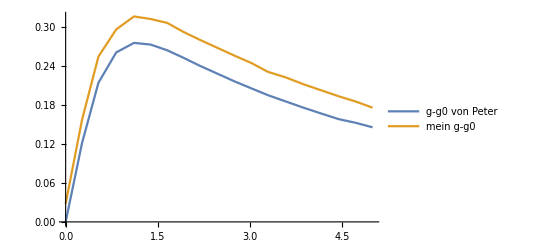

```mathematica
Plot[{gminusg0peter[t],-Re[gminusg0[t]]}, {t,0,5}, PlotRange -> Full,PlotPoints->10, MaxRecursion->1, PlotLegends->{"g-g0 von Peter", "mein g-g0",  "mein g-g0 interpol"}]
```

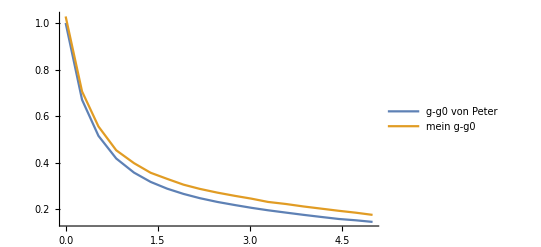

```mathematica
Plot[{gtotpeter[t],ghans[t]}, {t,0,5}, PlotRange -> Full,PlotPoints->10, MaxRecursion->1, PlotLegends->{"g-g0 von Peter", "mein g-g0",  "mein g-g0 interpol"}]
```

## G-G0 FT Peter

```mathematica
gminusg0peterw[w_]:= NIntegrate[gminusg0peter[t]*Exp[I*w*t], {t ,0,100}];
gminusg0peterw2[w_]:= NIntegrate[gtotpeter[t]*Exp[I*w*t], {t ,0,100}]-g0piw[p,w];
```

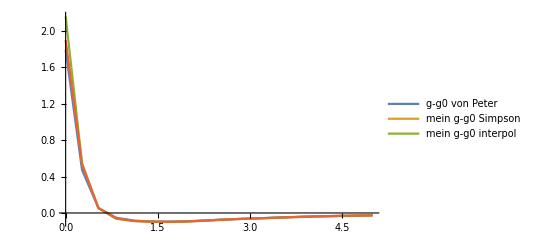

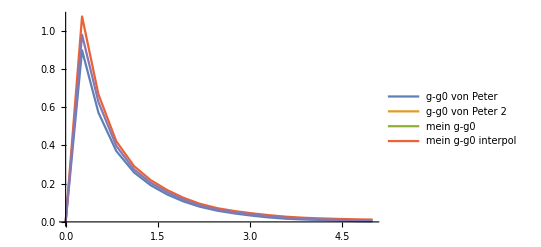

```mathematica
Plot[{Re[gminusg0peterw[w]],Re[gminusg0peterw2[w]],-Re[gminusg0w[w]],-Re[interpolgminusg0w[w]]}, {w,0,5}, PlotRange -> Full,PlotPoints->10, MaxRecursion->1, PlotLegends->{"g-g0 von Peter", "mein g-g0 Simpson", "mein g-g0 interpol"}]
Plot[{Im[gminusg0peterw[w]],Im[gminusg0peterw2[w]],,-Im[gminusg0w[w]],-Im[interpolgminusg0w[w]]}, {w,0,5}, PlotRange -> Full,PlotPoints->10, MaxRecursion->1, PlotLegends->{"g-g0 von Peter","g-g0 von Peter 2", "mein g-g0",  "mein g-g0 interpol"}]
```

## G-G0 Re FT Peter

```mathematica
list= Table[{w, gminusg0peterw[w]}, {w,-10,10,0.1}];
interpolgminusg0peterw=Interpolation[list];
```

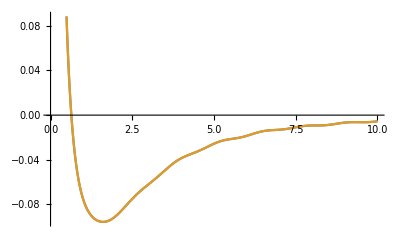

```mathematica
Plot[{Re[interpolgminusg0peterw[w]], Re[gminusg0peterw[w]]}, {w,0,10}]
regminusg0peter[t_]:= NIntegrate[interpolgminusg0peterw[w]/2/Pi*Exp[-(I*w*t)], {w,-10,10}];
```

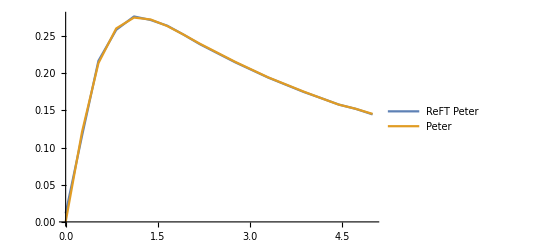

```mathematica
Plot[{regminusg0peter[t], gminusg0peter[t]}, {t,0,5}, PlotRange -> Full,PlotPoints->10, MaxRecursion->1, PlotLegends->{"ReFT Peter","Peter"}]
```